Auxiliary Modules, start them first, or evaluate the entire Worksheet

```mathematica
twoDigit[x_]:=Round[x,0.01]
zeros[x_]:=Round[x,0.0000000000001]
(* A module to generate group elements for a given set of generators, the list of rounded elements is used to avoid overcounting of equal elements due to floating point inaccuracies *)
maxNumberOfElements = 3000;
GroupOf[gens_]:=Module[{i,j,newElems={},tmpElems={},elements={},element,roundedElements,roundedElement},
newElems=N[gens,30];
elements=N[gens,30];
roundedElements = twoDigit[gens];
While[Length[newElems]>0 && Length[elements]<maxNumberOfElements,
tmpElems ={};
For[i=1,i≤Length[gens],i++,
For[j=1,j≤Length[newElems],j++,
element =N[newElems[[j]].gens[[i]],30];
roundedElement = twoDigit[element];
If[Not[MemberQ[roundedElements,roundedElement]],
tmpElems =Union[tmpElems,{element}];
elements =Union[elements,{element}];
roundedElements = Union[roundedElements,{roundedElement}]
]
]
];
newElems=tmpElems;
];
Return[elements]
]
(*The special point generation for the flat case *)
AffineGeneration[gens_,shift_,point_]:=Module[{newElems={},tmpElems={},elements={},element,roundedElements,roundedElement},
newElems={N[point,30]};
elements={N[point,30]};
roundedElements = {twoDigit[point]};
While[Length[newElems]>0 && Length[elements]<maxNumberOfElements/10,
tmpElems ={};
For[i=1,i≤Length[gens],i++,
For[j=1,j≤Length[newElems],j++,
element =N[gens[[i]].newElems[[j]],30];
If[i==1,element=element+shift];(*apply affine transformation*)
roundedElement = twoDigit[element];
If[Not[MemberQ[roundedElements,roundedElement]],
tmpElems =Union[tmpElems,{element}];
elements =Union[elements,{element}];
roundedElements = Union[roundedElements,{roundedElement}]
]
]
];
newElems=tmpElems;
];
Return[elements]
]
(* A module to find the shortest distances between a points *)
Edges[points_,g_]:=Module[{edges={},min=10000,i,j,dist,threshold,dotp,diff},
If[sgn==-1,threshold=1,threshold=0.001];
For[i=1,i≤Length[points],i++,
For[j=i+1,j≤Length[points],j++,
dotp = points[[i]].g.points[[j]];
If[geometry=="hyperbolic",dist =-dotp,If[geometry=="spherical", dist = ArcCos[dotp],diff = points[[i]]-points[[j]];
dist =diff.diff]];
If[dist<min  &&  dist>threshold*1.1,min=dist];
]
];
For[i=1,i≤Length[points],i++,
For[j=i+1,j≤Length[points],j++,
dotp = points[[i]].g.points[[j]];
If[geometry=="hyperbolic",dist =-dotp,If[geometry=="spherical", dist = ArcCos[dotp],diff = points[[i]]-points[[j]];
dist =diff.diff]];
If[dist≤ min*1.1,AppendTo[edges,{i,j}]];
]
];
Return[edges];
]
(* Plot for the output of vertices and edges *)
CustomPlot[points_,edges_]:=Module[{range},
If[geometry=="hyperbolic",range={{-10,10},{-10,10},{0,20}},If[geometry=="spherical",range = {{-1.2,1.2},{-1.2,1.2},{-1.2,1.2}},range={{-10,10},{-10,-10},{-10,10}}]];Graphics3D[{Table[{Blue,Sphere[points[[i]],0.2]},{i,1,Length[points]}],Table[{Red,Cylinder[{points[[edges[[i]][[1]]]],points[[edges[[i]][[2]]]]},0.1]},{i,1,Length[edges]}]},BoxRatios->{1,1,1},PlotRange->range]
]
(* Poincare disk projection *)
Poincare[points_,edges_]:=Module[{pPoints={}},
pPoints=Table[{(points[[i]][[1]])/(1+points[[i]][[3]]),(points[[i]][[2]])/(1+points[[i]][[3]])},{i,1,Length[points]}];
Graphics[{PointSize[Medium],Red,Point[Table[pPoints[[i]],{i,1,Length[pPoints]}]],{Yellow,Table[Line[{pPoints[[edges[[i]][[1]]]],pPoints[[edges[[i]][[2]]]]}],{i,1,Length[lines]}]}},Background->Black]
]
```

# Construct matrix represenations of Coxeter groups: {p,q}

Define the parameters of the Coxeter-Dynkin diagram

```mathematica
p=3
q=7
```

3

7

Determine the choice of geometry

```mathematica
geometry = "";
angle=(180-360/q)p
If[angle==360,geometry="flat",If[angle<360,geometry="spherical",geometry="hyperbolic"]]
```

2700/7

hyperbolic

Depending on the choice of geometry the metric and the scalar product are defined

```mathematica
If[geometry=="hyperbolic",sgn=-1,sgn=1];
g={{1,0,0},{0,1,0},{0,0,sgn}}
SProduct[v_,w_]:=v.g.w;
```

{{1,0,0},{0,1,0},{0,0,-1}}

The Coxeter-Dynkin diagram translates into a matrix, where the cosines of angles between two planes of reflexion are collected.
The dot product among the various normal vectors is contained inside the Coxeter matrix

The first and the last reflection generator are orthogonal. This means, that the matrices of both generators can be diagonal simultaneously. Before, we calculate the matrices, let’s write down the normal vectors of the planes of reflection. We choose the first to reflect along the x-axis and the third to reflect along the z-axis. The second is not specified yet.

```mathematica
coxeterM = {{1,Cos[π/p],0},{Cos[π/p],1,Cos[π/q]},{0,Cos[π/q],1}};
coxeterM//MatrixForm
Subscript[n, 1]={1,0,0};
Subscript[n, 3]={0,1,0};
Subscript[n, 2]={Subscript[n, x],Subscript[n, y],Subscript[n, z]};
eqs=Table[Subscript[n, i].g.Subscript[n, j]==coxeterM[[i,j]],{i,1,3},{j,i,3}];
nsol=Solve[Flatten[eqs]];
Subscript[N, 1]=Subscript[n, 1]
Subscript[N, 2]=Subscript[n, 2]/.nsol[[1]]
Subscript[N, 3]=Subscript[n, 3]
```

(1 | 1/2 | 0
1/2 | 1 | Cos[π/7]
0 | Cos[π/7] | 1)

{1,0,0}

{1/2,Cos[π/7],-1/2 √(-3+4 Cos[π/7]^2)}

{0,1,0}

The normal specifies the plane of reflection through the origin uniquely. From the reflection action of the plane, the corresponding reflection matrix can be calculated. We first need the dropped perpendicular foot and then find the reflected point x' = x-2(x.n) n
Consequently the reflection matrix is 1-2 n (n.g)^t

```mathematica
M=Table[IdentityMatrix[3]-2 TensorProduct[Subscript[N, i],Subscript[N, i].g],{i,1,3}];
M[[1]]//MatrixForm
M[[2]]//MatrixForm
M[[3]]//MatrixForm
```

(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

(1/2 | -Cos[π/7] | -1/2 √(-3+4 Cos[π/7]^2)
-Cos[π/7] | 1-2 Cos[π/7]^2 | -Cos[π/7] √(-3+4 Cos[π/7]^2)
1/2 √(-3+4 Cos[π/7]^2) | Cos[π/7] √(-3+4 Cos[π/7]^2) | 1+1/2 (-3+4 Cos[π/7]^2))

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

Let us check the properties, that are required for a representation of the Coxeter group {p,q}

```mathematica
{FullSimplify[MatrixPower[M[[2]].M[[3]],q]]//MatrixForm,FullSimplify[MatrixPower[M[[1]].M[[2]],p]]//MatrixForm,FullSimplify[MatrixPower[M[[1]].M[[3]],2]]//MatrixForm}
Table[FullSimplify[M[[i]].M[[i]]]//MatrixForm,{i,1,3}]
```

{(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}

{(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}

## Representations

Generate point group. This maybe doesn’t work for all choices of p and q out of the box. There is a list of rounded elements to make sure that every group element is only collected once.

```mathematica
group = GroupOf[M];
Length[group]
```

3069

If we start with a vector that is common to two planes of reflection, we generate the smallest representations of the reflection group

(1,2)-Version

{0.,-0.286926,1.04035}

Number of vertices: 678

Number of lines: 883

-Graphics3D-

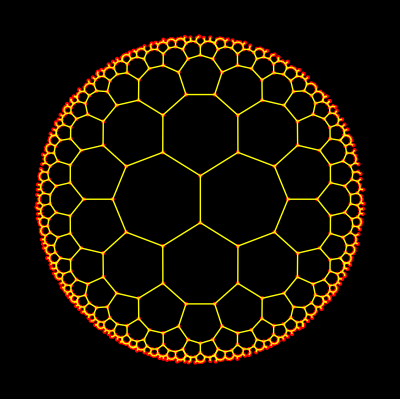

```mathematica
point = {Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]};
If[geometry=="flat",
shift = Cos[π/q];
eqs={Subscript[N, 1].g.point==shift,Subscript[N, 2].g.point==0,point.g.point==sgn};
,
eqs={Subscript[N, 1].g.point==0,Subscript[N, 2].g.point==0,point.g.point==sgn};
shift=0];
solutions=N[Solve[eqs]];
If[Length[solutions]>1,If[(Subscript[X, 3]/.solutions[[2]])>0,P={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}/.solutions[[2]],P={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}/.solutions[[1]]],P={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}/.solutions[[1]]]
If[geometry=="flat",points = AffineGeneration[M,{2*shift,0,0},P],points = Union[Table[zeros[N[group[[i]].P,4]],{i,1,Length[group]}]]];
Print["Number of vertices: ",Length[points]]
lines =Edges[points,g];
Print["Number of lines: ",Length[lines]]
CustomPlot[points,lines]
If[geometry=="hyperbolic",Poincare[points,lines]]
```

(2,3)-Version

{{X_1→-0.5727,X_2→0.,X_3→1.15238},{X_1→0.5727,X_2→0.,X_3→-1.15238}}

{-0.5727,0.,1.15238}

Number of vertices: 404

Number of lines: 1066

-Graphics3D-

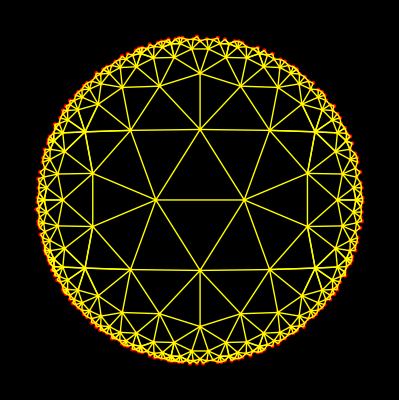

```mathematica
point = {Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]};
If[geometry=="flat",
shift = 1;
eqs={Subscript[X, 2]==0,Subscript[N, 1].g.point==shift,point.g.point==sgn};
,
shift=0;
eqs={Subscript[N, 2].g.point==0,Subscript[N, 3].g.point==0,point.g.point==sgn};
];
solutions=N[Solve[eqs]]
If[Length[solutions]>1,If[(Subscript[X, 3]/.solutions[[2]])>0,P={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}/.solutions[[2]],P={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}/.solutions[[1]]],P={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}/.solutions[[1]]]
If[geometry=="flat",points = AffineGeneration[M,{2*shift,0,0},P],points = Union[Table[zeros[N[group[[i]].P,4]],{i,1,Length[group]}]]];
Print["Number of vertices: ",Length[points]]
lines =Edges[points,g];
Print["Number of lines: ",Length[lines]]
CustomPlot[points,lines]
If[geometry=="hyperbolic",Poincare[points,lines]]
```

(1,3)-Version

{0.,0.,1.}

Number of vertices: 900

Number of lines: 1500

-Graphics3D-

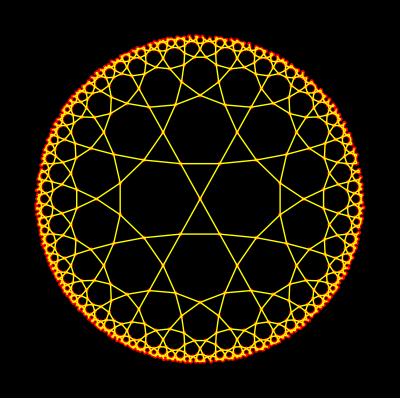

```mathematica
point = {Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]};
If[geometry=="flat",
shift =Cos[π/p];
eqs={Subscript[X, 2]==0,Subscript[N, 3].g.point==0,point.g.point==sgn};
,
shift=0;
eqs={Subscript[N, 1].g.point==shift,Subscript[N, 3].g.point==0,point.g.point==sgn};
];
solutions=N[Solve[eqs]];
If[Length[solutions]>1,If[(Subscript[X, 3]/.solutions[[2]])>0,P={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}/.solutions[[2]],P={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}/.solutions[[1]]],P={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}/.solutions[[1]]]
If[geometry=="flat",points = AffineGeneration[M,{2*shift,0,0},P],points = Union[Table[zeros[N[group[[i]].P,4]],{i,1,Length[group]}]]];
Print["Number of vertices: ",Length[points]]
lines =Edges[points,g];
Print["Number of lines: ",Length[lines]]
CustomPlot[points,lines]
If[geometry=="hyperbolic",Poincare[points,lines]]
```

```mathematica
Export["points73.csv",points]
Export["lines73.csv",lines]
```

points73.csv

lines73.csv